```mathematica
μ=5;
a=90*B;
o=20*B;
Y1[y_]:=2(1-y^2)(x^4(2*x^2+a*y))/((2*x^2+a*y)^2+(2*o*x)^2)
A1[B_ ]:=NIntegrate[Y1[y]*1/4 1/Cosh[(x-μ)/2]^2,{x,-10,20},{y,-1,1}]
Y2[y_]:=(2 a x^2 y (2 a^2-4 x^4+a x^2 y)+(a^2-4 x^4)^2 Log[Abs[2 x^2+a y]])/a^3
A2[B_ ]:=NIntegrate[(Y2[1]-Y2[-1])1/4 1/Cosh[(x-μ)/2]^2,{x,-10,20}]
Y3[y_]:=2(1-y^2)(2 x^5*o)/((2*x^2+a*y)^2+(2*o*x)^2)
A3[B_ ]:=NIntegrate[Y3[y]*1/4 1/Cosh[(x-μ)/2]^2,{x,-10,20},{y,-1,1}]
```

```mathematica
σ[B_,θ_]:=(Cos[θ]^2*A1[B]+Sin[θ]^2*A2[B])(A1[B](Cos[θ]^2*A2[B]+Sin[θ]^2*A1[B])+Sin[θ]^2*A3[B]^2)+Cos[θ]^2*A3[B]^2(Cos[θ]^2*A2[B]+Sin[θ]^2*A1[B]+Sin[θ]^2(A2[B]-A1[B]))+Sin[θ]^2*Cos[θ]^2(A2[B]-A1[B])(A3[B]^2-A1[B](A2[B]-A1[B]))
ρ[B_,θ_]:=(A1[B](A1[B]*Cos[θ]^2+A2[B]*Sin[θ]^2)+A3[B]^2 Cos[θ]^2)/σ[B,θ]
```

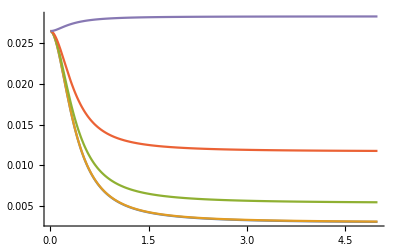

```mathematica
Plot[{ρ[B,0],ρ[B,π/80],ρ[B,π/10],ρ[B,π/5],ρ[B,π/2]},{B,0.001,5},BaseStyle->{FontFamily->"Times",FontSize->18},PlotRange->Full]
```

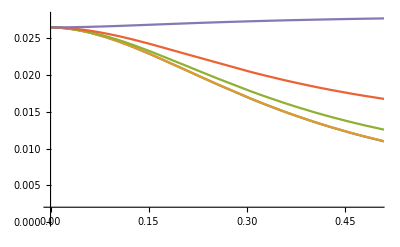

```mathematica
Show[%12,PlotRange->{{0,0.5},{0,0.028}}]
```

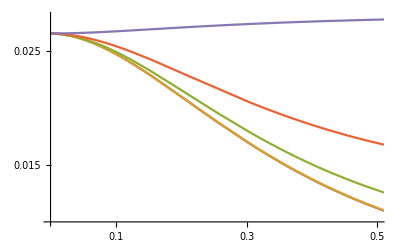

-Graphics-

```mathematica
Show[%12,BaseStyle->{FontFamily->"Times",FontSize->25},PlotRange->{{0,.5},{0.01,0.028}},Ticks->{{0.1,0.3,0.5},{0.005,0.015,0.025}},AxesOrigin->{0,0.01}]
```

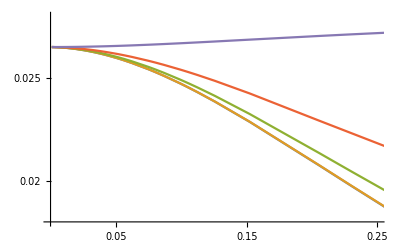

-Graphics-

```mathematica
Show[%14,BaseStyle->{FontFamily->"Times",FontSize->16},PlotRange->{{0,.25},{0.018,0.028}},Ticks->{{0.05,0.15,0.25},{0.02,0.025}},AxesOrigin->{0,0.018}]
```

```mathematica
μ=5;
a=45*B;
o=(20*B)/(1+0.9*B);
Y1[y_]:=2(1-y^2)(x^4(2*x^2+a*y))/((2*x^2+a*y)^2+(2*o*x)^2)
A1[B_ ]:=1/(1+0.9*B)NIntegrate[Y1[y]*1/4 1/Cosh[(x-μ)/2]^2,{x,-10,20},{y,-1,1}]
Y2[y_]:=(2 a x^2 y (2 a^2-4 x^4+a x^2 y)+(a^2-4 x^4)^2 Log[Abs[2 x^2+a y]])/a^3
A2[B_ ]:=NIntegrate[(Y2[1]-Y2[-1])1/4 1/Cosh[(x-μ)/2]^2,{x,-10,20}]
Y3[y_]:=2(1-y^2)(2 x^5*o)/((2*x^2+a*y)^2+(2*o*x)^2)
A3[B_ ]:=1/(1+0.9*B)NIntegrate[Y3[y]*1/4 1/Cosh[(x-μ)/2]^2,{x,-10,20},{y,-1,1}]
σ[B_,θ_]:=(Cos[θ]^2*A1[B]+Sin[θ]^2*A2[B])(A1[B](Cos[θ]^2*A2[B]+Sin[θ]^2*A1[B])+Sin[θ]^2*A3[B]^2)+Cos[θ]^2*A3[B]^2(Cos[θ]^2*A2[B]+Sin[θ]^2*A1[B]+Sin[θ]^2(A2[B]-A1[B]))+Sin[θ]^2*Cos[θ]^2(A2[B]-A1[B])(A3[B]^2-A1[B](A2[B]-A1[B]))
ρ[B_,θ_]:=(A1[B](A1[B]*Cos[θ]^2+A2[B]*Sin[θ]^2)+A3[B]^2 Cos[θ]^2)/σ[B,θ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {10.6954}. NIntegrate obtained 37.7199 and 0.0000544084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {10.6954}. NIntegrate obtained 37.7199 and 0.0000544084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {10.6954}. NIntegrate obtained 37.7199 and 0.0000544084 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

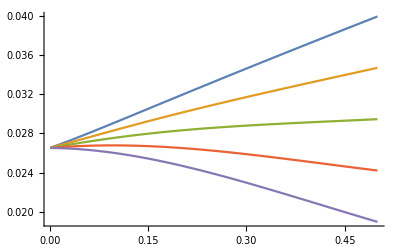

```mathematica
Plot[{ρ[B,π/2],ρ[B,π/3],ρ[B,π/4],ρ[B,π/6],ρ[B,0]},{B,0.001,0.5}]
```

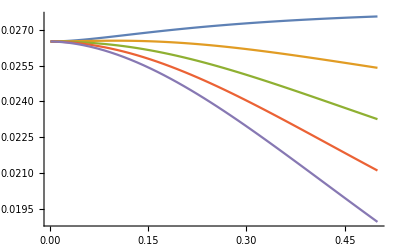

-Graphics-

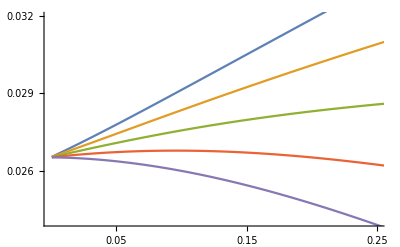

-Graphics-

```mathematica
Show[%10,BaseStyle->{FontFamily->"Times",FontSize->16},PlotRange->{{0,0.25},{0.024,0.032}},Ticks->{{0.05,0.15,0.25},{0.026,0.029,0.032}},AxesOrigin->{0,0.0238}]
```

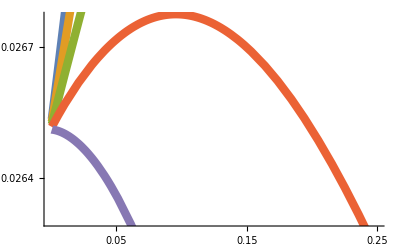

```mathematica
Show[%1,BaseStyle->{FontFamily->"Times",FontSize->32},PlotRange->{{0,.25},{0.0263,0.02677}},Ticks->{{0.05,0.15,0.25},{0.0264,0.0267}},AxesOrigin->{0.001,0.026277}]
```

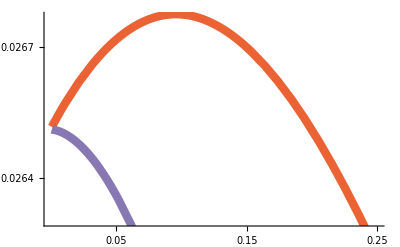

-Graphics-

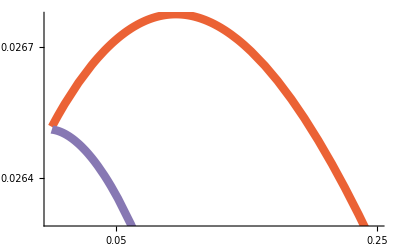

```mathematica
Show[%1,BaseStyle->{FontFamily->"Times",FontSize->40},PlotRange->{{0,.25},{0.0263,0.02677}},Ticks->{{0.05,0.25},{0.0264,0.0267}},AxesOrigin->{0.001,0.026277}]
```

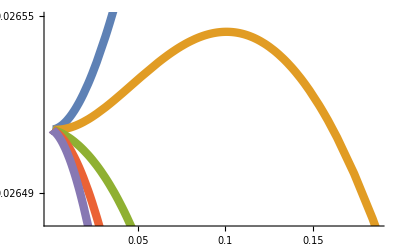

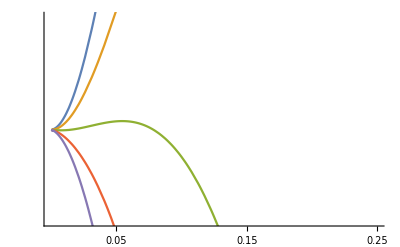

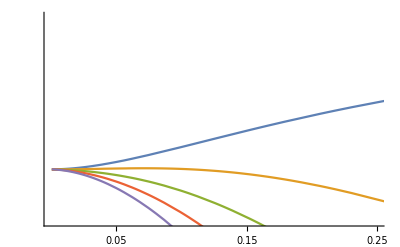

-Graphics-

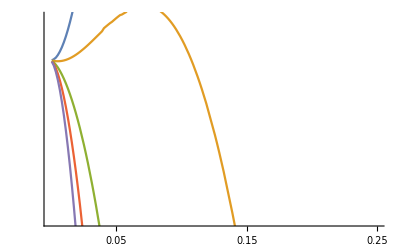

```mathematica
Show[%34,BaseStyle->{FontFamily->"Times",FontSize->25},PlotRange->{{0,.25},{0.02648,0.02652}},Ticks->{{0.05,0.15,0.25},{0.02,0.025}},AxesOrigin->{0,0.018}]
```

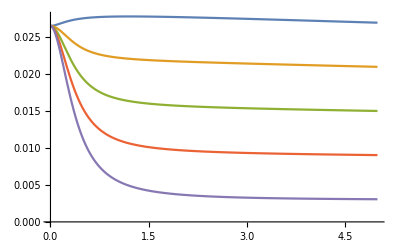

-Graphics-

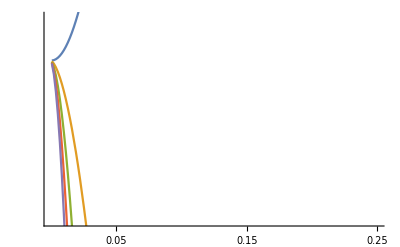

```mathematica
Show[%39,BaseStyle->{FontFamily->"Times",FontSize->25},PlotRange->{{0,.25},{0.02648,0.02652}},Ticks->{{0.05,0.15,0.25},{0.02,0.025}},AxesOrigin->{0,0.018}]
```